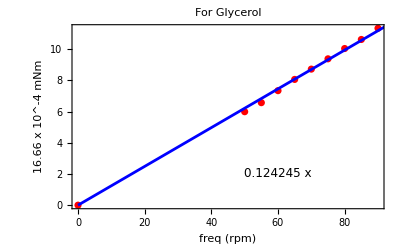

```mathematica
data={{0,0},{50,5.99},{55,6.57},{60,7.34},{65,8.06},{70,8.72},{75,9.38},{80,10.04},{85,10.62},{90,11.34}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Glycerol",Epilog->{Text[Style[eqn,12],{60,2}]}]
```

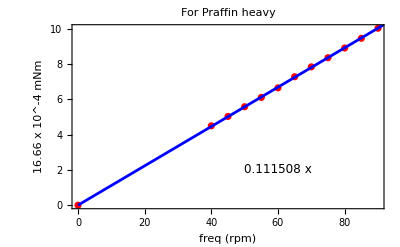

```mathematica
data={{0,0},{40,4.5},{45,5.03},{50,5.58},{55,6.11},{60,6.65},{65,7.28},{70,7.84},{75,8.36},{80,8.91},{85,9.46},{90,10.03}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Praffin heavy",Epilog->{Text[Style[eqn,12],{60,2}]}]
```